# nearest neighbor algorithm

## входные данные

### поле:

```mathematica
rows=40;
columns=60;
```

### дроны:

```mathematica
numberOfDrones=5;
turnsOfDrones=112993;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=5;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=100;
```

### склады:

```mathematica
numberOfWarehouses = 3;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehouses[rows,columns,numberOfWarehouses]
```

{{47,24},{59,15},{41,26}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}]
```

{{51,44,9,78,72},{61,91,53,84,62},{19,5,27,31,70}}

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{131,140,89,193,204}

### заказы:

```mathematica
numberOfOrders =5;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords]
```

{{30,15},{1,28},{12,4},{58,24},{1,5}}

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

30

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],3],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts]
```

{{0,3,2,0,3},{3,2,3,2,0},{0,3,2,2,0},{0,1,0,3,2},{0,1,1,1,1}}

```mathematica
And@@(#>0&/@(totalNumberOfProducts-Total@orders))
```

True

### база данных:

```mathematica
data=<|
"area"-> <|
"rows"->rows,
"columns"->columns
|>,

"drones"-><|
"number"->numberOfDrones,
"turns"->turnsOfDrones,
"capacity"->capacityOfDrones,
"drone"->AssociationThread[Range@numberOfDrones->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧,"score"->#⟦3⟧|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])],
"coords"->ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],
"products"->ConstantArray[0,{numberOfDrones,numberOfProducts}],
"score"->ConstantArray[0,numberOfDrones]
|>,

"products"-><|
"number"->numberOfProducts,
"weights"->productsWeights
|>,

"warehouses"-><|
"number"->numberOfWarehouses,
"warehouse"->AssociationThread[Range@numberOfWarehouses->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])]
|>,

"orders"-><|
"number"->numberOfOrders,
"order"->AssociationThread[Range@numberOfOrders->(<|"coords"->#⟦1⟧,"list"->#⟦2⟧|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders]
|>
|>;
```

## анализ данных

```mathematica
data⟦"warehouses","warehouse",All,"coords"⟧
```

<|1→{47,24},2→{59,15},3→{41,26}|>

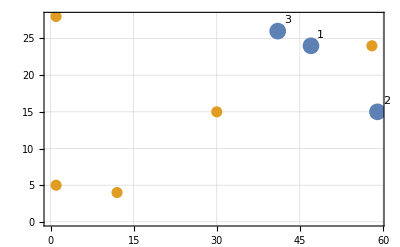

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses","warehouse",All,"coords"⟧,Range@data["warehouses","number"]}],Values@data⟦"orders","order",All,"coords"⟧},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}]
```

3 склада, расположенные в точках:

```mathematica
Values@data⟦"warehouses","warehouse",All,"coords"⟧//Column
```

{47,24}
{59,15}
{41,26}

где первый склад - начальный, то есть откуда стартуют дроны. Есть 5 типов продуктов, которые весят соответственно:

```mathematica
data["products","weights"]//Column
```

197
72
55
46
13

каждого продукта на каждом складе соответственно:

```mathematica
Values@data⟦"warehouses","warehouse",All,"products"⟧//Column
```

{51,44,9,78,72}
{61,91,53,84,62}
{19,5,27,31,70}

5 дронов, каждый из которых находится в первом складе и имеет грузоподъемность:

```mathematica
data["drones","capacity"]
```

200

необходимо доставить 5 заказов на данные точки:

```mathematica
Values@data⟦"orders","order",All,"coords"⟧//Column
```

{30,15}
{1,28}
{12,4}
{58,24}
{1,5}

каждому клиенту необходимо соответсвующих товаров:

```mathematica
Values@data⟦"orders","order",All,"list"⟧//Column
```

{0,3,2,0,3}
{3,2,3,2,0}
{0,3,2,2,0}
{0,1,0,3,2}
{0,1,1,1,1}

## алгоритм

Для каждого дрона определяем ближайший склад, где можно пополнить запас продуктов, а также ближайшего клиента от этого склада.  Среди всех дронов выбираем того, у которого сумма длин двух расстояний наименьшая и выполняем им весь заказ или его часть. Так до тех пор, пока все заказы не будут выполнены.

```mathematica
plot
```

-Graphics-

```mathematica
(*нужно сделать проверку, чтобы дрон выбирал склад только в том случае, если на нем есть хотя бы один нужный товар*)
```

```mathematica
Clear@chooseShortestPath
chooseShortestPath[coords_,data_Association]:=
Module[
{to,from},
to=MinimalBy[data⟦"warehouses","warehouse",All,"coords"⟧,N@EuclideanDistance[Value@#,coords]&];
from=MinimalBy[
Pick[data⟦"orders","order",All,"coords"⟧,data["orders","mask"],0],
N@EuclideanDistance[Value@to,Value@#]&];
{to,from}
]
```

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["drones","capacity"],weights=data["products","weights"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses","warehouse",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses","warehouse",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones","drone",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];

If[capacity≤0,Break[]]
,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones","drone",droneID,"products"⟧;
tempData⟦"drones","drone",droneID,"products"⟧=ConstantArray[0,data["products","number"]];
Print["дрон ",droneID, " отгрузил товар клиенту ", orderID];
If[DeleteDuplicates@tempData⟦"orders","order",orderID,"list"⟧=={0},tempData⟦"orders","mask",orderID⟧=1;Print["заказ ",orderID, " полностью выполнен"]];
tempData
]
```

```mathematica
-Graphics-;
```

```mathematica
plot
```

-Graphics-

```mathematica
tempData=data;
Module[
{nextDrone,nextWarehouse,nextOrder,score,orderList},
TimeConstrained[
While[
Times@@tempData["orders","mask"]≠1,

(*выбор дрона*)
nextDrone=First@Keys@MinimalBy[tempData⟦"drones","drone"⟧,Last@chooseShortestPath[#["coords"],tempData]&];
{nextWarehouse,nextOrder}=chooseShortestPath[tempData["drones","drone",nextDrone,"coords"],tempData];
Print["выбран дрон ",nextDrone];

(*перемещение дрона на ближайший склад*)
tempData["drones","drone",nextDrone,"score"]+=Ceiling@EuclideanDistance[tempData["drones","drone",nextDrone,"coords"],First@Values@nextWarehouse];
tempData["drones","drone",nextDrone,"coords"]=First@Values@nextWarehouse;
Print["дрон ",nextDrone," переместился к складу ",First@Keys@nextWarehouse," с координатами ",First@Values@nextWarehouse];

(*погрузка товара*)
tempData=loadProducts[tempData,First@Keys@nextWarehouse,First@Keys@nextOrder,nextDrone];

(*перемещаение дрона к ближайшему клиенту*)
tempData["drones","drone",nextDrone,"score"]+=Ceiling@EuclideanDistance[First@Values@nextOrder,First@Values@nextWarehouse];
tempData["drones","drone",nextDrone,"coords"]=First@Values@nextOrder;
Print["дрон ",nextDrone," переместился к клиенту ",First@Keys@nextOrder," с координатами ",First@Values@nextOrder];

(*разгрузка товара*)
tempData=unloadProduct[tempData,First@Keys@nextOrder,nextDrone]
],
1];
]
```

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 2 со склада 3 для заказа 5

дрон 1 загрузил 1 у.е. продукта 3 со склада 3 для заказа 5

дрон 1 загрузил 1 у.е. продукта 4 со склада 3 для заказа 5

дрон 1 загрузил 1 у.е. продукта 5 со склада 3 для заказа 5

дрон 1 переместился к клиенту 5 с координатами {1,5}

дрон 1 отгрузил товар клиенту 5

заказ 5 полностью выполнен

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 1 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 1 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 1 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 2 у.е. продукта 2 со склада 3 для заказа 2

дрон 1 загрузил 1 у.е. продукта 3 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 2 у.е. продукта 3 со склада 3 для заказа 2

дрон 1 загрузил 1 у.е. продукта 4 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 4 со склада 3 для заказа 2

дрон 1 переместился к клиенту 2 с координатами {1,28}

дрон 1 отгрузил товар клиенту 2

заказ 2 полностью выполнен

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 2 у.е. продукта 2 со склада 3 для заказа 3

дрон 1 загрузил 1 у.е. продукта 3 со склада 3 для заказа 3

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 загрузил 1 у.е. продукта 3 со склада 3 для заказа 3

дрон 1 загрузил 2 у.е. продукта 4 со склада 3 для заказа 3

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

выбран дрон 1

дрон 1 переместился к складу 3 с координатами {41,26}

дрон 1 переместился к клиенту 3 с координатами {12,4}

дрон 1 отгрузил товар клиенту 3

```mathematica
data⟦"warehouses","warehouse"⟧
```

<|1→<|coords→{47,24},products→{51,44,9,78,72}|>,2→<|coords→{59,15},products→{61,91,53,84,62}|>,3→<|coords→{41,26},products→{19,5,27,31,70}|>|>

```mathematica
tempData⟦"warehouses","warehouse"⟧
```

<|1→<|coords→{47,24},products→{51,44,9,78,72}|>,2→<|coords→{59,15},products→{61,91,53,84,62}|>,3→<|coords→{41,26},products→{16,0,21,26,69}|>|>

```mathematica
data⟦"orders","order",All,"list"⟧
```

<|1→{0,3,2,0,3},2→{3,2,3,2,0},3→{0,3,2,2,0},4→{0,1,0,3,2},5→{0,1,1,1,1}|>

```mathematica
tempData⟦"orders","order",All,"list"⟧
```

<|1→{0,3,2,0,3},2→{0,0,0,0,0},3→{0,1,0,0,0},4→{0,1,0,3,2},5→{0,0,0,0,0}|>

```mathematica
data⟦"drones","drone",All,"products"⟧
```

<|1→{0,0,0,0,0},2→{0,0,0,0,0},3→{0,0,0,0,0},4→{0,0,0,0,0},5→{0,0,0,0,0}|>

```mathematica
tempData⟦"drones","drone",All,"products"⟧
```

<|1→{0,0,0,0,0},2→{0,0,0,0,0},3→{0,0,0,0,0},4→{0,0,0,0,0},5→{0,0,0,0,0}|>